```mathematica
W := ((Subscript[ω, R]^6/(64 Subscript[λ, R]^3)+ (L(L+1))/(4 Subscript[λ, R]))/2+ √(((Subscript[ω, R]^6/(64 Subscript[λ, R]^3)+ (L(L+1))/(4 Subscript[λ, R]))^2)/4+ (((3 Subscript[ω, R]^4)/(16 Subscript[λ, R]^2))^3)/27))^(1/3) + ((Subscript[ω, R]^6/(64 Subscript[λ, R]^3)+ (L(L+1))/(4 Subscript[λ, R]))/2- √(((Subscript[ω, R]^6/(64 Subscript[λ, R]^3)+ (L(L+1))/(4 Subscript[λ, R]))^2)/4+ (((3 Subscript[ω, R]^4)/(16 Subscript[λ, R]^2))^3)/27))^(1/3)
Subscript[R, 0]:= √(W - 1/3 Subscript[ω, R]^2/(4 Subscript[λ, R]))
Λ:= Subscript[λ, R]+ 5/2(L(L+1))/Subscript[R, 0]^6
(*Choose some values for l, ω, λ*)
L={1,2,3,4};
Subscript[ω, R]=1.0;
Print[Λ]
```

{5/(((-√(1/4 (0.015625/λ_R^3+1/(2 λ_R))^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+1/(2 λ_R)))^(1/3)+(√(1/4 (0.015625/λ_R^3+1/(2 λ_R))^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+1/(2 λ_R)))^(1/3)-0.0833333/λ_R)^3)+λ_R,15/(((-√(1/4 (0.015625/λ_R^3+3/(2 λ_R))^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+3/(2 λ_R)))^(1/3)+(√(1/4 (0.015625/λ_R^3+3/(2 λ_R))^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+3/(2 λ_R)))^(1/3)-0.0833333/λ_R)^3)+λ_R,30/(((-√(1/4 (0.015625/λ_R^3+3/λ_R)^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+3/λ_R))^(1/3)+(√(1/4 (0.015625/λ_R^3+3/λ_R)^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+3/λ_R))^(1/3)-0.0833333/λ_R)^3)+λ_R,50/(((-√(1/4 (0.015625/λ_R^3+5/λ_R)^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+5/λ_R))^(1/3)+(√(1/4 (0.015625/λ_R^3+5/λ_R)^2+0.000244141/λ_R^6)+1/2 (0.015625/λ_R^3+5/λ_R))^(1/3)-0.0833333/λ_R)^3)+λ_R}

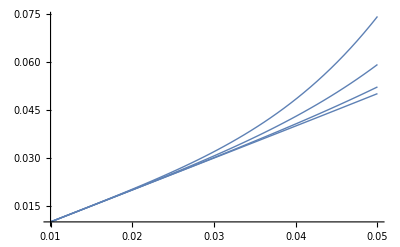

```mathematica
Plot[Re[Λ],{Subscript[λ, R], 0.01, 0.05},PlotStyle->Thick]
```

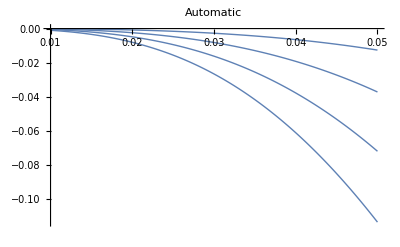

```mathematica
Plot[Im[Λ],{Subscript[λ, R], 0.01,0.05},PlotStyle->Thick, PlotLabel->Automatic, PlotPoints->200,PlotLegends->Automatic]
```